```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*ΓMathematica[[i, j, k]] = Γ^i_{k j}*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
(*\Nabla_r v^r*)
Δrvr[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
(*\Nabla_\theta v^theta*)
Δθvθ[r_]:=v[r]Γ[r][[2,2,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
N3dr[x_]:=-{Cos[x[[2]]], Sin[x[[2]]],0} 
N3dR[x_]:={Cos[x[[2]]], Sin[x[[2]]],0} 
N3dγ[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
```

```mathematica
Ntr[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dr[x].e[j][x],{j,1,2}],{i,1,2}]
NtR[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dR[x].e[j][x],{j,1,2}],{i,1,2}]
Ntγ[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dγ[x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
Ntr[{r,θ}]//FullSimplify
NtR[{r,θ}]//FullSimplify
Ntγ[{r,θ}]//FullSimplify
```

{-1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

```mathematica
nr[x_]:=Ntr[x]/Sqrt[Sum[Ntr[x][[i]] Ntr[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nR[x_]:=NtR[x]/Sqrt[Sum[NtR[x][[i]] NtR[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nγ[x_]:=Ntγ[x]/Sqrt[Sum[Ntγ[x][[i]] Ntγ[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
nγ[{r,θ}]
```

{√(1/(1+z'[r]^2)),0}

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in \Nalba_i \Nabla^i H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] ϕ'[r]
```

```mathematica
(*fVISC[r] = f^{VISC r}_notes*)
```

```mathematica
fVISCt[r_]:=(2 η (v''[r]+(v'[r] z'[r] z''[r])/(1+z'[r]^2)-(2 v[r] z'[r]^2 z''[r]^2)/((1+z'[r]^2)^2)+(v[r] z''[r]^2)/(1+z'[r]^2)+(-v[r]/r+v'[r]+(v[r] z'[r] z''[r])/(1+z'[r]^2))/r+(v[r] z'[r] Derivative[3][z][r])/(1+z'[r]^2)))/(1+z'[r]^2)
```

```mathematica
fσt[r_]:=ig[r][[1,1]]σ'[r]
```

```mathematica
fvt[r_]:=ρ v[r]Δrvr[r]
```

```mathematica
(*d[r][[i,j]] = d_{ij}_notes*)
```

```mathematica
d[r_]:={{g[r][[1,1]]Δrvr[r],0},{0,g[r][[2,2]]Δθvθ[r]}}
```

```mathematica
(*Π[r_][[i,j]]= \Pi^{ij}_notes*)
```

```mathematica
Π[r_]:=Table[Table[-σ[r]ig[r][[i,j]]-2 η ig[r][[i,i]]ig[r][[j,j]]d[r][[i,j]],{j,1,2}],{i,1,2}]
```

```mathematica
(*force per unit length exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdl[r_]:=Table[Sum[Π[r][[i,j]] g[r][[j, k]]*nγ[{r,θ}][[k]],{j,1,2},{k,1,2}],{i,1,2}]
```

```mathematica
(*relation between v and z' given by the continuity equation*)
```

```mathematica
repv={v[r]->C1/(r √(1+(z'[r])^2)),v'[r]->-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2)),v''[r]->(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r Derivative[3][z][r])+r z'[r]^3 (2 z''[r]-r Derivative[3][z][r])))/(r^3 (1+z'[r]^2)^(5/2))};
```

```mathematica
FullSimplify[D[D[C1/(r √(1+(z'[r])^2)),r],r],Assumptions->ass]
```

(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r z^(3)[r])+r z'[r]^3 (2 z''[r]-r z^(3)[r])))/(r^3 (1+z'[r]^2)^(5/2))

```mathematica
eqs=FullSimplify[{   
ρ v[r]Δrvr[r]==ig[r][[1,1]]σ'[r]+2 η ig[r][[1,1]]( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] +2 η (ig[r][[1,1]]Δrvr[r]b[r][[1,1]] + ig[r][[2,2]]Δθvθ[r]b[r][[2,2]])
},Assumptions->ass]
```

```mathematica
eqs=FullSimplify[eqs/.repv,Assumptions->ass]
```

```mathematica
Clear[κ,η,ρ]
```

```mathematica
Clear[C1]
```

```mathematica
Rmin=1;
Rmax=2;
```

```mathematica
κ=1;
η=1;
ρ=1;
```

```mathematica
(*values to be entered in variational+problem_bc_ring.py:
-vRmin = v_r_const_{variational+problem_bc_ring.py}
  - vRmax (to be determined by the solution of the ODE) = v_R_const_{variational_problem_bc_ring.py}
 -σRmax = sigma_R_const_{variational+problem_bc_ring.py}
- zRmax = z_R_const_{variational+problem_bc_ring.py}
- zpRmin = omega_r_const_{variational+problem_bc_ring.py}
- zpRmax = omega_R_const_{variational+problem_bc_ring.py}
*)
vRmin=0.0099995000374968752734129;
σRmax=0;
zRmax=0.5;
zpRmin=0.1;
zpRmax=0;
```

```mathematica
zRmin=0.4581171976058265;
```

```mathematica
solC1=Solve[vRmin==C1/(Rmin √(1+zpRmin^2)),C1][[1]]
```

{C1→0.0100494}

```mathematica
C1=C1/.solC1
```

0.0100494

```mathematica
bcs={
σ[Rmax]==σRmax,
z[Rmin]==zRmin,z[Rmax]== zRmax,z'[Rmin]==zpRmin,z'[Rmax]==zpRmax
};
```

```mathematica
bcs
```

{σ[2]==0,z[1]==0.458117,z[2]==0.5,z'[1]==0.1,z'[2]==0}

```mathematica
Flatten[{eqs,bcs}]
```

```mathematica
sol=NDSolve[Flatten[{eqs,bcs}],{σ,z},{r,Rmin,Rmax},WorkingPrecision->30][[1]]
```

NDSolve::precw: The precision of the differential equation ({{σ'[r]/(1+Power[«2»])+(0.0100494 (0.0100494 Power[«2»]+2 r («1»)^(«1»)[«1»] Power[«2»] («1»)^(«1»)[«1»]))/r^3==0,«5»,z'[2]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

{σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
vRmax= v[r]/.repv/.sol/.{r->Rmax}
```

0.00502469

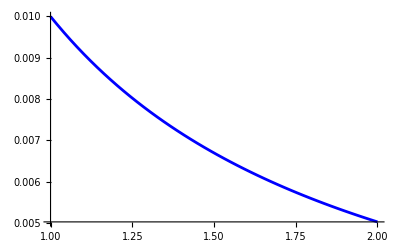

```mathematica
plotvODE=Plot[{v[r]/.repv/.sol},{r,Rmin,Rmax},PlotStyle->Blue]
```

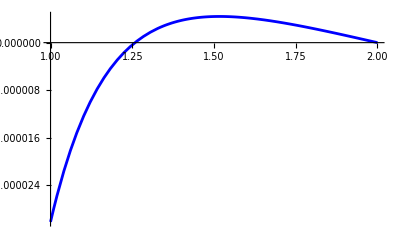

```mathematica
plotσODE=Plot[Evaluate[σ[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

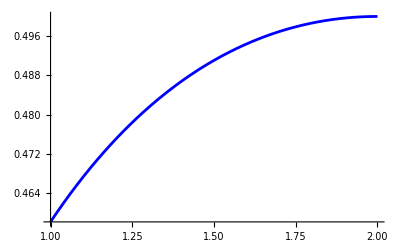

```mathematica
plotzODE=Plot[Evaluate[z[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

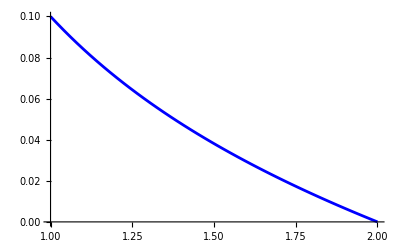

```mathematica
plotωODE=Plot[z'[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

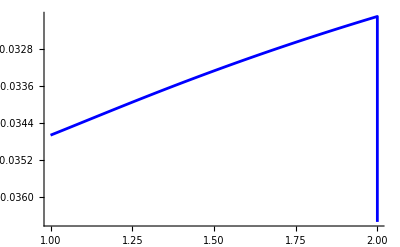

```mathematica
plotμODE=Plot[H[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
delta=1/100;
```

```mathematica
(*Compare with the solution from FE*)
```

```mathematica
(*check of v*)
```

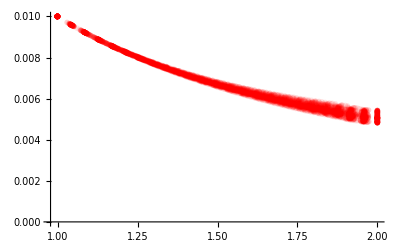

```mathematica
tabv=Import["~/Documents/finite_elements/steady-state-flow/solution/v.csv"];
tabv=Table[{Norm[{tabv[[i,4]],tabv[[i,5]]}],({tabv[[i,4]],tabv[[i,5]]}/Norm[{tabv[[i,4]],tabv[[i,5]]}]).{tabv[[i,1]],tabv[[i,2]]}},{i,2,Length[tabv]}]
plotvfe=ListPlot[tabv,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

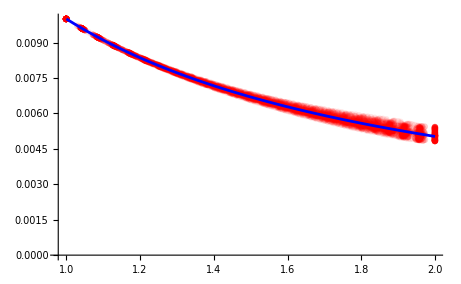

```mathematica
Show[plotvfe,plotvODE]
```

```mathematica
(*res = 0.15*)
```

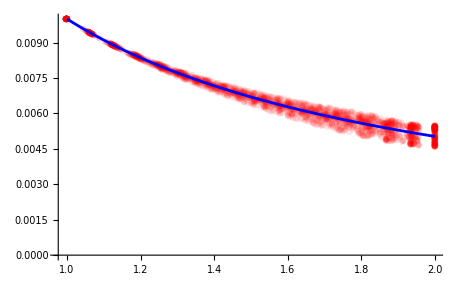

-Graphics-

```mathematica
(*res = 0.1*)
```

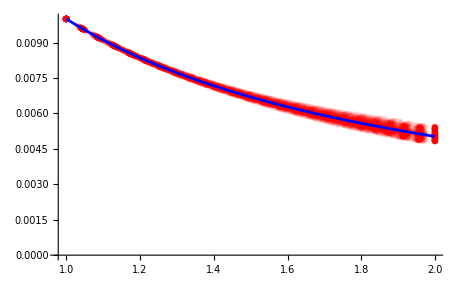

-Graphics-

```mathematica
(*res = 0.05*)
```

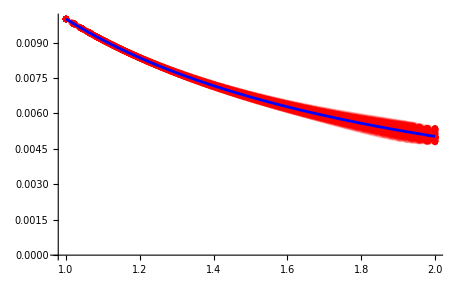
```mathematica
-Graphics-;
```

```mathematica
(*check of sigma*)
```

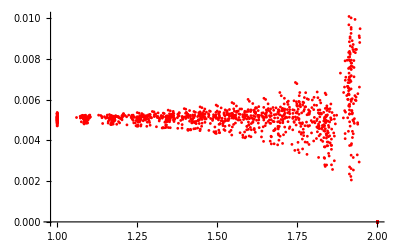

```mathematica
tabσ=Import["~/Documents/finite_elements/steady-state-flow/solution/sigma.csv"];
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,2,Length[tabσ]}]
plotσfe=ListPlot[tabσ,PlotRange->Full,PlotStyle->{PointSize->.005,Red,Opacity[1]}]
```

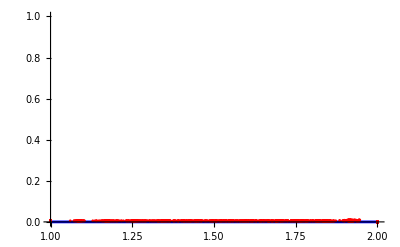

```mathematica
Show[plotσODE,plotσfe,PlotRange->{0,1}]
```

```mathematica
(*check of z*)
```

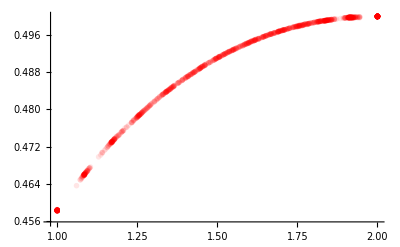

```mathematica
tabz=Import["~/Documents/finite_elements/steady-state-flow/solution/z.csv"];
tabz=Table[{Norm[{tabz[[i,2]],tabz[[i,3]]}],tabz[[i,1]]},{i,2,Length[tabz]}]
plotzfe=ListPlot[tabz,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

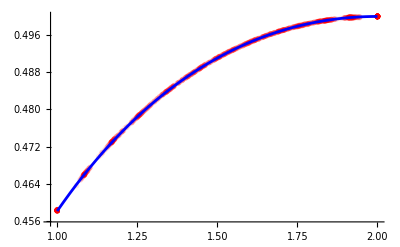

```mathematica
Show[plotzfe,plotzODE]
```

```mathematica
(*check of ω*)
```

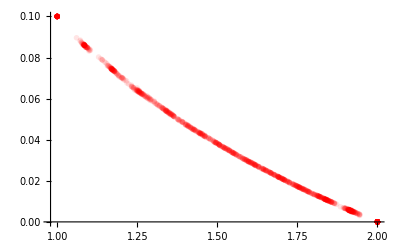

```mathematica
tabω=Import["~/Documents/finite_elements/steady-state-flow/solution/omega.csv"];
tabω=Table[{Norm[{tabω[[i,4]],tabω[[i,5]]}],({tabω[[i,4]],tabω[[i,5]]}/Norm[{tabω[[i,4]],tabω[[i,5]]}]).{tabω[[i,1]],tabω[[i,2]]}},{i,2,Length[tabω]}]
plotωfe=ListPlot[tabω,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

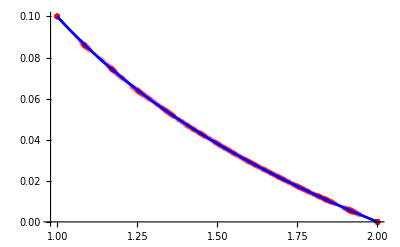

```mathematica
Show[plotωfe,plotωODE]
```

```mathematica
(*check of μ*)
```

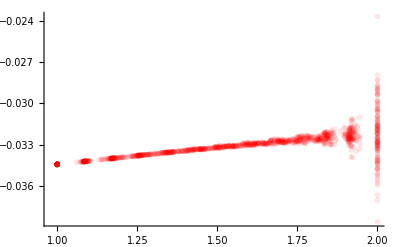

```mathematica
tabμ=Import["~/Documents/finite_elements/steady-state-flow/solution/mu.csv"];
tabμ=Table[{Norm[{tabμ[[i,2]],tabμ[[i,3]]}],tabμ[[i,1]]},{i,2,Length[tabμ]}]
plotμfe=ListPlot[tabμ,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

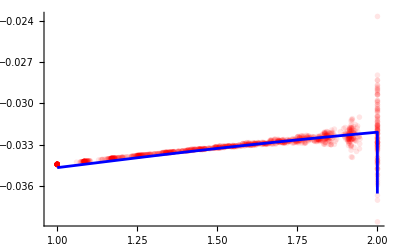

```mathematica
Show[plotμfe,plotμODE]
```

```mathematica
(*res = 0.15*)
```

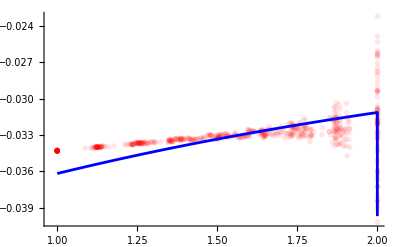

-Graphics-

```mathematica
(*res = 0.1*)
```

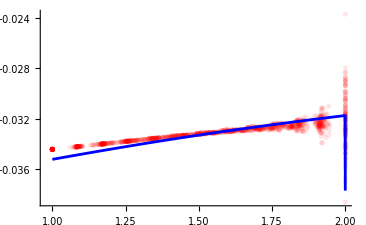
```mathematica
-Graphics-;
```

```mathematica
(*res = 0.05*)
```

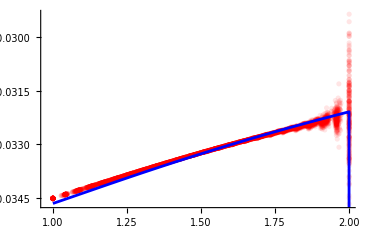
```mathematica
-Graphics-;
```

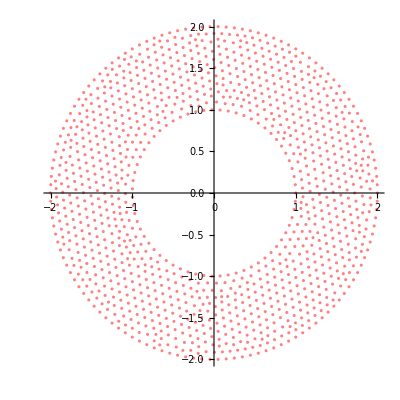

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution/vertices.csv"];
tabve=Drop[tabve,{1}]
ListPlot[tabve,PlotStyle->Pink,AspectRatio->1]
```

```mathematica
tabz=Table[{z[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]]},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution/zODE.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution/zODE.csv